## Pressure calculations for the deterministic wall model

```mathematica
Started 10/11/2015
To do: grid spacing
```

#### Functions

```mathematica
Δ[θ_,θ0_,α_?NumericQ]:=α Log[θ/θ0]-θ+θ0
θ0[θ_?NumericQ,δ_?NumericQ,α_?NumericQ]:=θ0/.FindRoot[Δ[θ,θ0,α]==δ,{θ0,α+θ}]//Re
ρ[θ_,θ0_?NumericQ,α_?NumericQ]:=(θ0(√(θ0^2+(θ0-α)^2))/(θ^2+(θ-α)^2)(√((θ-α)^2))/(θ0-α))*1/(√(2π))Exp[-θ0^2/2]HeavisideTheta[θ0-α]
```

#### Alphas to consider

```mathematica
aa=Table[i,{i,0.1,5.1,0.1}];
(*aa={0.1,0.5,1.0};*)
inds=Table[i,{i,1,Length[aa]}];
```

#### 2D density

```mathematica
ctplt=ContourPlot[ρ[θ,θ0[θ,δ,#],#],
{δ,0,0.5},{θ,0,2*#},
PlotRange->All,
FrameLabel->{Style["Δ",Bold,FontSize->16],Style["η",Bold,FontSize->16]},
PlotLabel->Style["α="<>ToString[#],FontSize->16],ImageSize->Medium]&/@aa;
(*Export[NotebookDirectory[]<>"Pressure/PDFs2D.pdf",ctplt];*)
```

#### Marginalise at selected points

```mathematica
npoints=30;df=3.0;dd=df/npoints;
deltas=Table[δ,{δ,0.0,df,dd}];
points=Table[NIntegrate[ρ[θ,θ0[θ,δ,aa[[#]]],aa[[#]]],{θ,0,5},MaxRecursion->12],{δ,0.0,df,dd}]&/@inds;
(*deltas=Table[δ^2,{δ,0.0,√df,dd/√df}];
points=Table[NIntegrate[ρ[θ,θ0[θ,δ,aa[[#]]],aa[[#]]],{θ,0,5},MaxRecursion->12],{δ,0.0,√df,dd/√df}]&/@inds;*)
lgdata=MapThread[Flatten@*List,{deltas,#}]&/@Log[points];
lndata=MapThread[Flatten@*List,{deltas,#}]&/@points;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in θ near {θ} = {0.100598}. NIntegrate obtained 0.652727 and 1.10444×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in θ near {θ} = {0.100598}. NIntegrate obtained 0.668238 and 1.43494×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in θ near {θ} = {0.100598}. NIntegrate obtained 0.668081 and 1.68251×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

#### Plot marginalised pdf with fits

```mathematica
lfit=a+b x/.FindFit[lgdata[[#]],a+b x,{{a,0.01},{b,-2}},x]&/@inds;
qfit=a+c x^2/.FindFit[lgdata[[#]],a+c x^2,{{a,0.01},{c,-1}},x]&/@inds;
ftplt=Show[
ListPlot[lgdata,AxesLabel->{"Δ","Log[p(Δ)]"},
PlotLegends->aa],
ListPlot[TemporalData[lfit/.(x->deltas),{deltas}],Joined->True],
ListPlot[TemporalData[qfit/.(x->deltas),{deltas}],Joined->True,PlotStyle->{Dashed}],
ImageSize->Large];
(*Export[NotebookDirectory[]<>"Pressure/PDF_fits.pdf",ftplt]*)
```

```mathematica
lfit=a+b x/.FindFit[lgdata[[#]],a+b x,{{a,0.01},{b,-2}},x]&/@inds;
qfit=a+c x^2/.FindFit[lgdata[[#]],a+c x^2,{{a,0.01},{c,-1}},x]&/@inds;
lgplt=Show[
ListPlot[lgdata],
ListPlot[TemporalData[lfit/.(x->deltas),{deltas}],Joined->True],
PlotRange->All,
AxesLabel->{"Δ","Log[p(Δ)]"}
];
lnplt=ListPlot[lndata,PlotRange->All,AxesLabel->{"Δ","p(Δ)"}];
pdf=GraphicsRow[{lnplt,lgplt},PlotRange->All,ImageSize->Full];
(*Export[NotebookDirectory[]<>"Pressure/pdf.pdf",pdf];*)
```

#### Pressure

```mathematica
f=Interpolation[lndata[[#]]]&/@inds;
prs=Show[
Plot[
aa[[#]]*NIntegrate[f[[#]][x],{x,0,δ}]&/@inds//Evaluate,
{δ,0,df},
AxesLabel->{"Δ","P(Δ)"},GridLines->Automatic,
PlotLegends->aa]//Quiet,
Plot[{aa[[#]]*NIntegrate[f[[#]][x],{x,0,df}]&/@inds//Evaluate},{x,0,df},PlotStyle->{Dashed}],
ImageSize->Large
];
(*Export[NotebookDirectory[]<>"Pressure/pressure.pdf",prs];*)
```

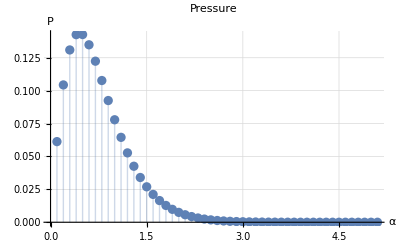

```mathematica
f=Interpolation[lndata[[#]]]&/@inds;
pra=ListPlot[
{aa,aa*NIntegrate[f[[#]][x]&/@inds,{x,0,1}]}//Transpose,
PlotRange->All,
Filling->Axis,GridLines->Automatic,PlotLabel->"Pressure",AxesLabel->{"α","P"}]
(*Export[NotebookDirectory[]<>"Pressure/pressure_alpha.pdf",pra];*)
```

```mathematica
f=Interpolation[lndata[[#]]]&/@inds;
PP=aa*NIntegrate[f[[#]][x]&/@inds,{x,0,1}];
```

```mathematica
fitfunc=a Exp[-b x] x^c;
Pfit=fitfunc/.FindFit[{aa,PP}//Transpose,fitfunc,{a,b,c},x]
```

1.72918 ⅇ^(-3.1132 x) x^1.35082

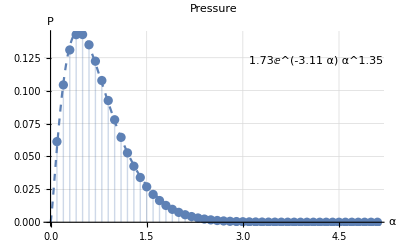

C:\Users\user\Dropbox\NYU\Grosberg\Code\Coloured_Noise\Pressure/pressure_alpha_fit.pdf

```mathematica
Show[
{ListPlot[
{aa,PP}//Transpose,
PlotRange->All,
Filling->Axis,GridLines->Automatic,
PlotLabel->"Pressure",AxesLabel->{"α","P"}],
Plot[Pfit,{x,0,5},PlotStyle->Dashed,
PlotLegends->Placed["1.73ⅇ^(-3.11 α) α^1.35",{0.8,0.85}]]}
]
Export[NotebookDirectory[]<>"Pressure/pressure_alpha_fit.pdf",pra]
```